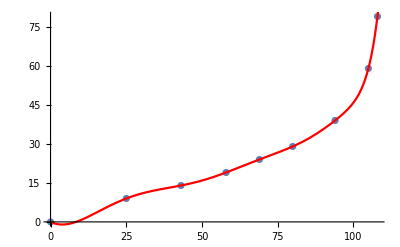

5.3191055520428166e-14 - 0.5575420423471357*(ball_dist) + 0.08675983374944524*(ball_dist)**2 - 0.0026342555302766436*(ball_dist)**3 + 0.00002216602021047992*(ball_dist)**4 + 1.6845456015846015e-7*(ball_dist)**5 - 1.2338278646316668e-9*(ball_dist)**6 - 2.159139461237281e-11*(ball_dist)**7 - 7.729815511490796e-14*(ball_dist)**8 + 1.0927625444579813e-15*(ball_dist)**9 + 1.852070605232141e-17*(ball_dist)**10 + 1.1126190720947463e-19*(ball_dist)**11 - 4.609693323595001e-22*(ball_dist)**12 - 1.6781040254018216e-23*(ball_dist)**13 - 1.321869413241422e-25*(ball_dist)**14 + 1.536469436628114e-27*(ball_dist)**15

```mathematica
(*Input format is {dist to edge of bot, pixel distance}*)
data={{-9,0},{0,25.02},{5,43.1},{10,58},{15,69},{20,80},{30,94},{50,105},{70,108}};
data[[All,1]]+=9; data=Reverse/@data;
n=15; (*what order polynomial to fit*)
bestFit=Fit[data,Table[x^k,{k,0,n}],x];
Show[ListPlot[data,PlotRange->All],Plot[{bestFit},{x,0,120},PlotStyle->Red]]
bestFit/.{x->ball_dist};
pythonStr=ToString[bestFit/.{x->ball_dist},InputForm];
pythonStr=StringReplace[pythonStr,"*^"->"e"];
pythonStr=StringReplace[pythonStr,"^"->"**"];
pythonStr
```